## Introducing Mathematica (Appendix A)

### Variables have types

What is the color blue plus the number 3?  This does not make sense, as they are not the same type of thing.  Similarly, variables can be described as having a type (what Mathematica refers to as a `Head`).  The common types  in Mathematica include:

Integers

(Real) Numbers

Strings

Lists

Associations (aka “dictionaries”)

```mathematica
Head[3] (**)
```

```mathematica
Head[3.]
```

```mathematica
Head["3"]
```

### Data structures

Variables do not have to store a single thing, and it is often useful to compose data-structures which define the structure of the problem.  Two common data structures that we use are Lists and Associations.

#### Lists are variables containing ordered collections of values

```mathematica
x={"one","II",3,4.0}
```

```mathematica
x[[1]]
```

```mathematica
x[[1;;3]]
```

```mathematica
First[x]
```

```mathematica
Length[x]
```

```mathematica
Append[x,"next"]
```

#### Associations ("dictionaries") are unordered collections of key - value pairs. Given a key it returns a value.

```mathematica
myDictionary=<|
"apple"-> "a type of fruit",
3->"a number"|> (*keys can be any type of variable*)
```

```mathematica
myDictionary["apple"]
```

```mathematica
Keys[myDictionary]
```

```mathematica
Values[myDictionary]
```

### Functions perform operations on variables.

#### Applying functions to arguments

First we illustrate this with built in functions.

```mathematica
Sin[1.]
```

```mathematica
Cos[Sin[1.]] (*notice how functions can be nested!*)
```

```mathematica
NumericQ[1] (* built-in functions that end in Q return logical True/False results *)
```

```mathematica
NumericQ["two"]
```

#### Function arguments can be variables

```mathematica
x=2.
Sin[x]
```

#### Functions are composable

It is natural to apply a sequence of functions, and we can do this in different ways. The way that we use primarily in ICPC is to nest one function inside the other.

```mathematica
Cos[Sin[1.]]
```

However, matching the brackets can be tedious.  Mathematica offers a Prefix operator “@” which can be used to apply a function to the following item.  For example, we can rewrite the above as:

```mathematica
Cos@Sin[1.]
```

In principle, we can prefix everything, all the way down to the initial input:

```mathematica
Cos@Sin@1.
```

An analogy that I like to use is to say that this is like Shoe@Sock@Foot—put the Shoe on the Sock on the Foot.  The order matters, and the Shoe goes on last.

#### The (infamous) post-fix operator

A pre-fix operator implies the existence of a post-fix operator.  From the computer’s perspective, it makes no difference whether we say “Put the Shoe on the Sock on the Foot” or “Start with a foot, then apply a sock, then apply a shoe”.  In the latter case, temporally later operations are applied later in our verbal description.  That’s all a post-fix operator does:  Foot // Sock //Shoe.  Or:

```mathematica
1.//Sin//Cos
```

Why would you want to do this?  I like to use the postfix for operations that are not the central goal of the line of code, but are merely aftereffects to clean it up.  I don’t want to put them first, because it would detract from a clear statement of the goal.  In particular, ICPC uses this extensively for converting rational fractions and other symbolic style expressions into numerical representations by using the N function.

#### Defining your own functions

At its heart, Mathematica is a pattern-matching language.  The delayed assignment  “:=” looks for a pattern on the left hand side and replaces it with the pattern on the right-hand side.    By adding an underscore after the input argument name, we are telling the interpretter to match this pattern:

```mathematica
Clear[addOne]
addOne[input_]:=input+1
```

```mathematica
addOne[1]
```

#### Anonymous functions

We often must define functions to do individual tasks as needed:

```mathematica
addOne[x_]:=x+1
addOne@Sin[1.]
```

1.84147

But for “trivial” functions, which we don’t anticipate needing again, we might prefer to define anonymous functions; these do not have a defined name, but still act as functions.  The “slot” for the incoming variable is “#” and we end the anonymous function with an “&”.  For example:

```mathematica
(#+1)&@Sin[1.]
```

1.84147

This is especially useful for composing functions that have multiple arguments, such as:

```mathematica
SphericalHarmonicY[1,1,#,0]&@Range[0,Pi,0.1]
```

{0.,-0.0344919,-0.0686391,-0.102101,-0.134542,-0.165639,-0.195081,-0.222573,-0.247842,-0.270635,-0.290723,-0.307907,-0.322014,-0.332904,-0.340467,-0.344629,-0.345347,-0.342614,-0.336459,-0.326941,-0.314157,-0.298234,-0.279331,-0.257637,-0.233369,-0.206769,-0.178103,-0.147657,-0.115736,-0.0826592,-0.0487561,-0.0143659}

#### Restricting argument types

We can restrict the pattern match by specifying a data type (Head) after the underscore.  This can allow us to match specific data types and take different actions.

An additional use case is to use the “? after the underscore to perform a test on the argument; if the test returns True, then the pattern is matched, otherwise it does not.

```mathematica
addOne[input_String]:=input<>"one"
addOne[input_?NumericQ]:=input+1
addOne[input_List]:=Append[input,1]
```

```mathematica
(* we now have multiple patterns that can match *)
?addOne
```

```mathematica
addOne["two"]
```

twoone

```mathematica
addOne[2]
```

3

```mathematica
addOne[{5,6}]
```

{5,6,1}

In general, patterns are matched in the order they are defined, and from most specific to least specific.

#### Providing default values to functions

In addition to providing conditions for the pattern, it is also useful to define default values to an input argument parameter.  If the argument is not specified, then it will take the default value and proceed with the pattern evaluation.

```mathematica
add[input_?NumericQ,amount_:1]:=input+amount
```

```mathematica
add[2]
```

```mathematica
add[2,2]
```

### Applying functions to lists with Map

How would you apply the addOne function to each element in the list?  This is not the same as applying the function to a list:

```mathematica
addOne[{1,2,3}]  (*based on the above, this will Append the value one to the end...*)
```

{1,2,3,1}

The slightly more traditional “procedural” approach is to use the Table function

```mathematica
Table[
addOne[i],
{i,{1,2,3}}]
```

A  “functional” approach is to think about the function Map-ing on to each element in the list:

```mathematica
Map[addOne, {1,2,3}] (*assumes addOne only has one argument*)
```

{2,3,4}

```mathematica
Map[addOne[#]&,{1,2,3}] (*define the argument "slot" as a pure anonymous function*)
```

{2,3,4}

```mathematica
addOne/@{1,2,3} (*abbreviated form of map*)
```

{2,3,4}

```mathematica
addOne/@Range[3] (*use a function to defined the range 1, 2, 3*)
```

{2,3,4}

### Defining multi-step functions

So far, we have defined “simple” functions that work directly on their input arguments:

```mathematica
f[x_,y_]:=(Sqrt[x]+Sin[y])^2+1 (*returned value*)
```

What if we wanted to do some type of intermediate calculation?  This requires functions with multiple steps.  One of the simplest ways to do this is to define new constants (variables that don’t change during a given evaluation), using With:

```mathematica
f[x_,y_]:=With[
{a=Sqrt[x]+Sin[y]},
a^2+1 (*returned value*)]
```

To implement more complicated functions, we may need to define new internal variables that can be assigned new or different values during the course of the calculation.  Each statement (step in the calculation) is followed by a semicolon which suppresses the output:

```mathematica
f[x_,y_]:=Module[{a,b}, (*variables we will use*)
a=Sqrt[x]+Sin[y]; (*semicolon suppresses output*)
b=a^2;
b+1 (*returned value*)
]
```

In general, “With” can be easier to debug, as constants that are defined at the beginning cannot be redefined.  It is also faster than Module.  On the other hand, if we have multiple dependencies, this requires us to nest the With statements, which can get complicated or ugly:

```mathematica
f[x_,y_]:=With[
{a=Sqrt[x]+Sin[y]},
With[
{b=a^2},
b+1 (*returned value*)
]]
```

My heuristic: If you can use a single With, that’s always the best choice.  In other cases, you have a choice.  I tend to use With more than Module in my own research codes, as it is easier to debug (the fact that it is “locked” to an initial value means it cannot be inadvertently changed) and executes faster.  Often the solution is to break things up into multiple function, each of which is simple enough to be described using a single With.

### Plotting

Since writing the book, a function, “ListLinePlot” has been added, which eliminates the need to type the option “Joined → True”:

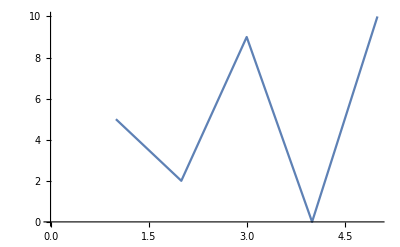

```mathematica
examplePoints = RandomInteger[{0,10},5];

ListPlot[examplePoints,Joined->True]; (*old way*)
ListLinePlot[examplePoints] (*new way*)
```

There’s no great advantage, other than concision.

Last edited: 31 January 2023